```mathematica
n[t_,af_,at_,tf_,tt_,t0_,s_,c_]:=af/(2*tf)*Exp[(s^2-2*tf*(t-t0))/(2*tf^2)]*(Erf[(s^2+tf*t0)/(Sqrt[2]*s*tf)]+Erf[(s^2+tf*(t-t0))/(Sqrt[2]*s*tf)])+at/(2*tt)*Exp[(s^2-2*tt*(t-t0))/(2*tt^2)]*(Erf[(s^2+tt*t0)/(Sqrt[2]*s*tt)]+Erf[(s^2+tt*(t-t0))/(Sqrt[2]*s*tt)])+c;
```

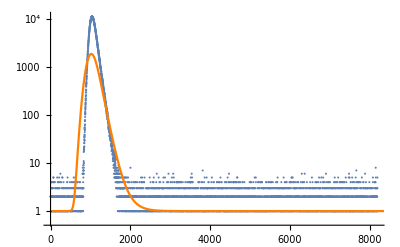

```mathematica
data=Import["Pseudodata/1.txt","Table"];
Show[ListLogPlot[data],Plot[Log[n[t,10000,80000,200,100,1150,100,1]],{t,0,10000},PlotStyle->{Orange},PlotRange->{{0,10000},{0,10000}}]]
```

```mathematica
nlm=NonlinearModelFit[data,n[t,af,at,tf,tt,t0,s,c],{{af,10000},{at,80000},{tf,200},{tt,100},{t0,1150},{s,100},{c,1}},t];
```

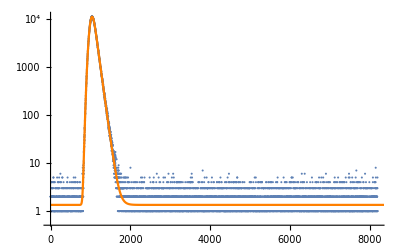

```mathematica
Show[ListLogPlot[data],Plot[Log[nlm[t]],{t,0,10000},PlotStyle->{Orange},PlotRange->{{0,10000},{0,10000}}]]
```

```mathematica
nlm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
af | 700810. | 12881.2 | 54.4057 | 3.8014250166×10^-551
at | 45430.4 | 10008.6 | 4.53913 | 5.72937×10^-6
tf | 72.3644 | 0.342377 | 211.359 | 2.9443837686×10^-3318
tt | 50.29 | 0.794591 | 63.2903 | 1.3590957898×10^-710
t0 | 1068.78 | 0.315943 | 3382.83 | 1.5593280643×10^-12878
s | 48.3385 | 0.0968576 | 499.067 | 3.4760489388×10^-6131
c | 1.34548 | 0.164834 | 8.16265 | 3.76573×10^-16